## The Main Function

In the following I construct a module LinearFitCom that helps us to visualize the linear fit of data pairs (x,y) as well as the (1-α) confidence interval bound based on the t statistics. In addition to the best fit line from simple least square fit I also plot two dashed lines, which provide a area enclosing estimators at the confidence level (1-α). 
The first two arguments of the function take the independent variable and the dependent variable in the form of lists/arrays respectively. The third argument is the type I error threshold value α. The last two arguments take the label on the horizontal and vertical axes.

```mathematica
LinearFitCom[xdata_,ydata_,alpha_,h_:"x",v_:"y"]:=Module[{XMat,VarMat,xydata,lm,S,t},
xydata=MapThread[{#1,#2}&,{xdata,ydata}];
XMat = MapThread[{1,#} &,{xdata}];
VarMat = Inverse[Dot[Transpose[XMat],XMat]];
lm = LinearModelFit[xydata,x,x,ConfidenceLevel->1-alpha];
Print[lm];
Print[lm["ParameterConfidenceIntervalTable"]];
Print[lm["ANOVATable"]];
Print[lm["ParameterTStatistics"]];
S = lm["EstimatedVariance"];
t = InverseSurvivalFunction[StudentTDistribution[Length[xdata]-2],alpha/2];
Show[ListPlot[xydata,PlotStyle->PointSize[Medium],PlotTheme->"Classic"],Plot[lm[x],{x,Min[xdata],Max[xdata]},PlotTheme->"Classic",PlotStyle->Blue],Plot[lm[x]+t*Sqrt[S]*Sqrt[1+Dot[{1,x},Dot[VarMat,{1,x}]]],{x,Min[xdata],Max[xdata]},PlotStyle->{Red,Thickness[0.004],Dashing[Tiny]},PlotTheme->"Classic"],Plot[lm[x]-t*Sqrt[S]*Sqrt[1+Dot[{1,x},Dot[VarMat,{1,x}]]],{x,Min[xdata],Max[xdata]},PlotStyle->{Red,Thickness[0.004],Dashing[Tiny]},PlotTheme->"Classic"],PlotRange->All,AxesLabel->{Style[h,FontSize->16,Italic],Style[v,FontSize->16,Italic]},LabelStyle->{FontFamily->"Times New Roman",14}]
]
```

## RLC circuit

Here I first present the linear relationships between X_Land ω and X_C^-1and ω in a RLC circuit at the (two-tailed) level of α = 1%.

### RL circuit

First we examine the RL circuit with the inductor with L = 7.92mH.

```mathematica
freqData = {9900,8470,7050,6080,4610};
RData = {494,412,342,300,228};
```

```mathematica
Processedfreq = MapThread[#/1000*(2*Pi)&, {freqData}];
```

FittedModel[-4.13529+7.91886 x]

| Estimate | Standard Error | Confidence Interval
1 | -4.13529 | 9.97121 | {-62.3762,54.1056}
x | 7.91886 | 0.212954 | {6.67501,9.16271}

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 41802.1 | 41802.1 | 1382.77 | 0.0000427774
Error | 3 | 90.6918 | 30.2306 |  | 
Total | 4 | 41892.8 |  |  |

{-0.414723,37.1857}

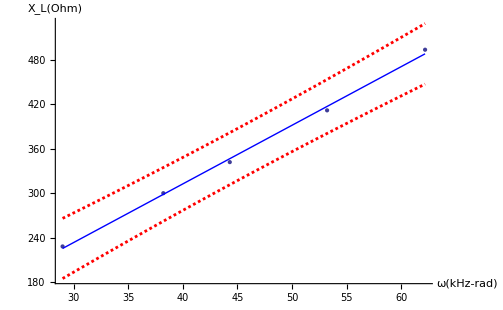

```mathematica
LinearFitCom[Processedfreq,RData,0.01,"ω(kHz-rad)","X_L(Ohm)"]
```

### RC circuit

Next we examine the RC circuit with the capacitor with C = 0.011 μF, and after adjusting the unit, we expect a slope of 1/C=90.91.

```mathematica
freqDataRC = {4610,5680,6960,8140,10920};
XcData = {3300,2700,2200,1900,1400};
```

```mathematica
ProcessedRCf = MapThread[1000/#/(2*Pi)&,{freqDataRC}];
```

FittedModel[27.4085+95057.3 x]

| Estimate | Standard Error | Confidence Interval
1 | 27.4085 | 21.4517 | {-97.8889,152.706}
x | 95057.3 | 862.266 | {90020.9,100094.}

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 2.13947×10^6 | 2.13947×10^6 | 12153.1 | 1.64555×10^-6
Error | 3 | 528.129 | 176.043 |  | 
Total | 4 | 2.14×10^6 |  |  |

{1.27769,110.241}

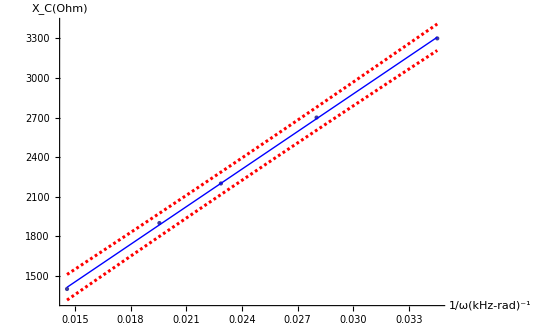

```mathematica
LinearFitCom[ProcessedRCf,XcData,0.01,"1/ω(kHz-rad)^-1","X_C(Ohm)"]
```

## e/mratio of electrons

As the second example I present the result I obtained for the charge to mass ratio of electrons. The parameters involved here depends on the design of the experiment and one may have to consult the manual. Here we plot a composite measurement (8 V_a D^2)/L^4as a function of B^2. After adjusting the unit, the literature value of e/m is a straight line of slope 1.76.

```mathematica
DisPlacementData ={0.005,0.01,0.015,0.02,0.025};
```

```mathematica
BData = {0.0000234,0.0000468,0.0000702,0.0000936,0.000117};
```

```mathematica
BsqData = MapThread[#^2*10^11 &,{BData}];
ProcessedXvar = MapThread[#^2*8*609/(0.19)^4 &,{DisPlacementData}];
```

FittedModel[-4.92883×10^-13+1.70687 x]

| Estimate | Standard Error | Confidence Interval
1 | -4.92883×10^-13 | 2.60124×10^-13 | {-2.01224×10^-12,1.02648×10^-12}
x | 1.70687 | 3.39502×10^-16 | {1.70687,1.70687}

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 3.26691×10^6 | 3.26691×10^6 | 2.52765×10^31 | 0
Error | 3 | 3.87741×10^-25 | 1.29247×10^-25 |  | 
Total | 4 | 3.26691×10^6 |  |  |

{-1.8948,5.02757×10^15}

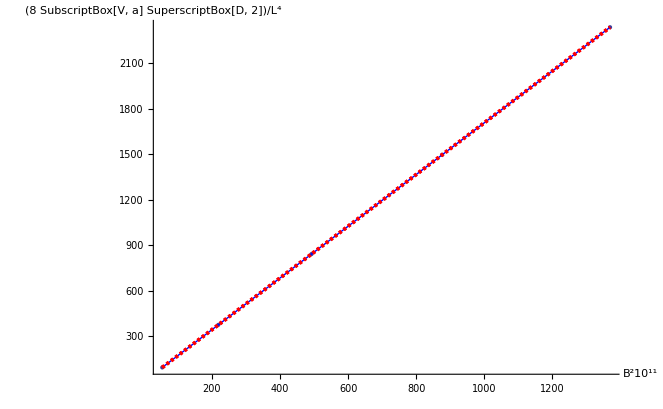

```mathematica
LinearFitCom[BsqData,ProcessedXvar,0.01,"B^210^11","(8 SubscriptBox[V, a] SuperscriptBox[D, 2])/L^4"]
```

## Electron deflection

The last example presented here is the study of the deflection of an electron in electric field. The electron is accelerated horizontally with the potential V_a and then in enters a region between 2 horizontally placed parallel plate capacitor. It can be shown the vertical displacement D is linearly proportional to vertical voltage V_d. Here we plot the result for V_a=300 volt.

```mathematica
VdData300 = {19.06,17.8,15.05,12.05,10, 8.01};
```

```mathematica
DData300 = {15.9,15.7,15.4,15,14.8,14.6};
```

FittedModel[13.6271+0.117573 x]

| Estimate | Standard Error | Confidence Interval
1 | 13.6271 | 0.0477693 | {13.4072,13.847}
x | 0.117573 | 0.00335552 | {0.102124,0.133022}

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 1.329 | 1.329 | 1227.71 | 3.9592×10^-6
Error | 4 | 0.00433003 | 0.00108251 |  | 
Total | 5 | 1.33333 |  |  |

{285.269,35.0386}

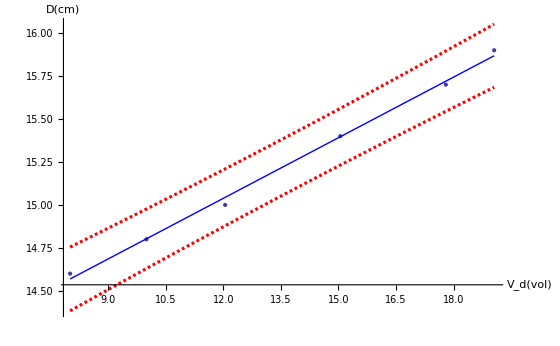

```mathematica
LinearFitCom[VdData300,DData300,0.01,"V_d(vol)","D(cm)"]
```